```mathematica
Framed[Graphics[Disk[Dynamic[MousePosition[{"Graphics",Graphics},{0,0}]]],PlotRange->2]]
```

-Graphics-

```mathematica
grid={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

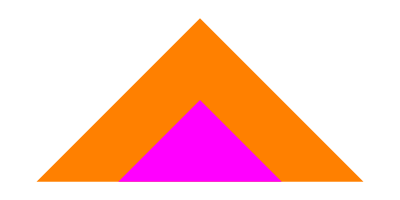

```mathematica
back=Show[
Graphics[{Orange,Polygon[{{1,0},{0,1},{-1,0}}]}],Graphics[{Magenta,Polygon[{{0.5,0},{0,0.5},{-0.5,0}}]}]
]
```

{{0.1,0,0,0.3},{1,1,0,0.3},{1,0,1,0.7},{1,0,1,0.7}}

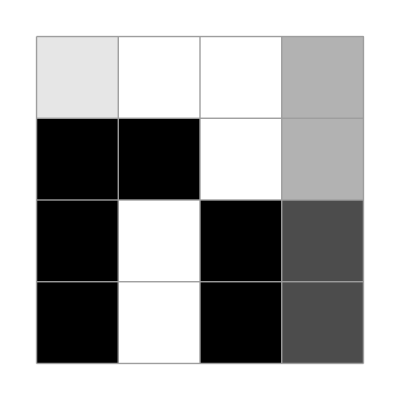

```mathematica
m={{0.1,0,0,0.3},{1,1,0,0.3},{1,0,1,0.7},{1,0,1,0.7}}
ArrayPlot[m,Mesh->True]
```

```mathematica
m={
{0.1,0.1,0,0},
{1,0,0,0},
{1,0,1,0},
{1,0,1,0}
} ;
m//MatrixForm

SetAttributes[AddIfEqual,HoldAll]
AddIfEqual[mat_,r1_,c1_,r2_,c2_]:=
Module[{},
If[mat[[r1,c1]]==mat[[r2,c2]],
Module[{},mat[[r2,c2]]=mat[[r1,c1]]+mat[[r2,c2]];mat[[r1,c1]]=0],
Module[{},Print["Not Equal"]]
]
Print["DONE"]
]

r1=1;
c1=1;
r2=1;
c2=2;
m[[r1,c1]]
m[[r2,c2]]
m[[r1,c1]]+m[[r2,c2]]

AddIfEqual[m,r1,c1,r2,c2]
m//MatrixForm
```

(0.1 | 0.1 | 0 | 0
1 | 0 | 0 | 0
1 | 0 | 1 | 0
1 | 0 | 1 | 0)

0.1

0.1

0.2

DONE

0

(0 | 0.2 | 0 | 0
1 | 0 | 0 | 0
1 | 0 | 1 | 0
1 | 0 | 1 | 0)